# 2.1 Degenerate linear system

#### Consider the dynamical system with a real parameter . Since the system is linear, it may be written in the form , where and is a . In the following consider general values a) For taking each of the values {−1,0,1}, plot a set of representative trajectories, for example using StreamPlot[] or NDSolve[] in Mathematica. Classify the fixed point in each of the cases and write your classification in the plots. Upload the three separate plots in one .pdf or .png file.

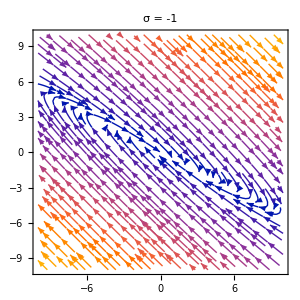
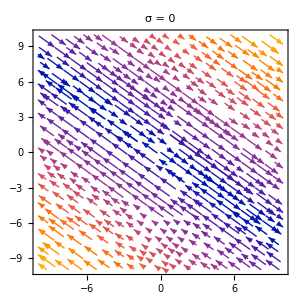
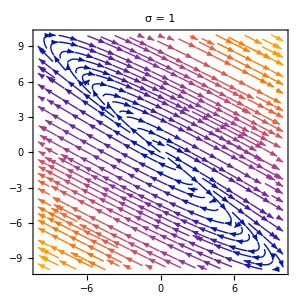
-Graphics-This is stable degenerate node.-Graphics-Not an isolated fix point. (Most probably a line of fix points.)-Graphics-This is an unstable degenerate node.

```mathematica
f[x_, y_] := (s + 3) x + 4 y
g[x_, y_] := -(9/4) x + (s - 3) y

valuesOfS = {-1, 0, 1};

plots = Table[
  Labeled[
    StreamPlot[{f[x, y], g[x, y]}, {x, -10, 10}, {y, -10, 10}, 
     StreamPoints -> Fine, StreamScale -> Automatic, 
     StreamStyle -> Blue,
     PlotLabel -> "σ = " <> ToString[s], ImageSize -> 300],
    Switch[s, 
      -1, "This is stable degenerate node.",
      0, "Not an isolated fix point. (Most probably a line of fix points.)",
      1, "This is an unstable degenerate node."
    ],
    Top
  ],
  {s, valuesOfS}
];

combinedPlot = Row[plots, Spacer[20]]
```

Using the Jacobian to determine the stability of the fix points gives the following analysis. See at the end of the file.

#### b) Analytically compute the eigenvalues, and , of in terms of . Write your result on the form: with .

```mathematica
A = {{sigma + 3, 4}, {-9/4, sigma - 3}};
{Lambda1, Lambda2} = Eigenvalues[A];

Print[Style["Eigenvalue 1: ", Darker@Green], Style[Lambda1, Darker@Green]]
Print[Style["Eigenvalue 2: ", Darker@Green], Style[Lambda2, Darker@Green]]
```

Eigenvalue 1: sigma

Eigenvalue 2: sigma

#### c) Analytically compute all the eigenvectors of . Remind yourself that an eigenvector is always non-zero by definition. For definiteness, normalise the vectors to one and choose the x-components positive. Write your answer as either a vector of vectors , one vector , or zero depending on how many eigenvectors you find.

```mathematica
A = {{sigma + 3, 4}, {-9/4, sigma - 3}};
{v1, v2}= Eigenvectors[A];
v1=-Normalize[v1]//MatrixForm;
v2=-Normalize[v2]//MatrixForm;
Print[Style["Eigenvector 1: ", Darker@Green], MatrixForm[Style[v1, Darker@Green]]]
Print[Style["Eigenvector 2: ", Darker@Green], MatrixForm[Style[v2, Darker@Green]]]
```

Eigenvector 1: (4/5
-3/5)

Eigenvector 2: (0
0)

#### d) Analytically compute the inverse matrix . Write your result as a matrix .

```mathematica
A = {{sigma + 3, 4}, {-9/4, sigma - 3}};
inv = Inverse[A]//Simplify//MatrixForm;
Print[Style["Inverse matrix A: ", Darker@Green], MatrixForm[Style[inv, Darker@Green]]]
```

Inverse matrix A: ((-3+sigma)/sigma^2 | -4/sigma^2
9/(4 sigma^2) | (3+sigma)/sigma^2)

#### e) Give the value of for which is singular ( does not exist).

```mathematica
A = {{sigma + 3, 4}, {-9/4, sigma - 3}};
detA = Det[A];
{sigmaSing1, sigmaSing2} = Solve[detA==0,sigma];
Print[Style["Sigma such that A is singular: ", Darker@Green], MatrixForm[Style[sigmaSing1, Darker@Green]]]
```

Sigma such that A is singular: {sigma→0}

#### Now consider the generalized problem for . This system has the same eigenvalues as the dynamical system above, and it simplifies to the system above if and . f) Analytically calculate one of the following: the stable direction for , the direction of the line of fixed points for, the unstable direction for . For definiteness, assume that c is positive, write the vector in terms of c and d with no minus signs and normalise it to one.

```mathematica
ClearAll[B, sol1, eigVec]

B[sigma_] := {{sigma - c*d, d^2}, {-c^2, sigma + c*d}}

sol1 = Eigenvectors[B[0]];

eigVec = sol1[[1]];

n = Normalize[eigVec];

Print[Style["Eigenvector:", Darker@Green], Style[eigVec, Darker@Green]];
Print[Style["Norm:", Darker@Green], Style[n, Darker@Green]];

normalizedEigVec = eigVec/n // Simplify;

Print[Style["Normalized Eigenvector:", Darker@Green], Style[normalizedEigVec, Darker@Green]];
```

Eigenvector:{d/c,1}

Norm:{d/(c √(1+Abs[d/c]^2)),1/(√(1+Abs[d/c]^2))}

Normalized Eigenvector:{√(1+Abs[d/c]^2),√(1+Abs[d/c]^2)}